```mathematica
ClearAll["Global`*"]
```

```mathematica
sRGB2XYZ={{0.4124, 0.3576, 0.1805},{0.2126, 0.7152,0.0722},{0.0193,0.1192,0.9505}}
```

{{0.4124,0.3576,0.1805},{0.2126,0.7152,0.0722},{0.0193,0.1192,0.9505}}

```mathematica
(* sRGB coordinate; Color name; circle color in plot *)

colorData={
gold={{212,175,55},"Gold"},
royalBlue={{65,105,225},"Royal Blue"},
red={{255,0,0},"Red"},
green={{0,255,0},"Green"},
(*cyan={{0,255,255},"Cyan"},*)
blue={{0,0,255},"Blue"},
(*yellow={{255,255,0},"Yellow"},
purple={{128,0,128},"Purple"},*)
white={{255,255,255},"white"}
};

(*colorData={gold,skyBlue,red,green,blue,yellow};*)
sRGB=colorData[[All,1]];
colorName=colorData[[All,2]];
colors=RGBColor@@@(sRGB/255)
```

{RGBColor[Rational[212, 255], Rational[35, 51], Rational[11, 51]],RGBColor[Rational[13, 51], Rational[7, 17], Rational[15, 17]],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 1, 1]}

```mathematica
XYZ0=sRGB2XYZ.Transpose[sRGB]
```

{{159.936,104.967,105.162,91.188,46.0275,242.377},{174.202,105.16,54.213,182.376,18.411,255.},{77.2291,227.633,4.9215,30.396,242.378,277.695}}

```mathematica
XYZ0T=Transpose@XYZ0
sumXYZ=Total@XYZ0
```

{{159.936,174.202,77.2291},{104.967,105.16,227.633},{105.162,54.213,4.9215},{91.188,182.376,30.396},{46.0275,18.411,242.378},{242.377,255.,277.695}}

{411.368,437.76,164.297,303.96,306.816,775.073}

```mathematica
XYZ1=MapThread[#1/#2&,{XYZ0T,sumXYZ}]
```

{{0.388792,0.423471,0.187737},{0.239781,0.240223,0.519996},{0.640074,0.329971,0.029955},{0.3,0.6,0.1},{0.150017,0.0600066,0.789977},{0.312716,0.329001,0.358283}}

```mathematica
assoLabel=MapThread[#1->#2&,{XYZ1[[All,1;;2]],colorName}];

plotCirclesNames=ListPlot[assoLabel,PlotStyle->Opacity[0],PlotMarkers->{Graphics[{EdgeForm[Black],Disk[]}],.04}];
plotCircles=ListPlot[Keys@assoLabel,PlotStyle->Opacity[0],PlotMarkers->{Graphics[{EdgeForm[Black],Disk[]}],.04}];

plot1=ChromaticityPlot["XYZ"];
plot2=ChromaticityPlot["sRGB"];
plot3=Show[ChromaticityPlot["XYZ"],plotCirclesNames];
plot4=Show[ChromaticityPlot["XYZ"],plotCircles];
plot5=Show[ChromaticityPlot["sRGB",WhitePoint->None],plotCirclesNames];

GraphicsGrid[{{plot1,plot2},{plot3,plot5}},ImageSize->700]
```

-Graphics-

```mathematica
img3Dress=Import[StringJoin[NotebookDirectory[],"Three dresses.jpg"]];
```

```mathematica
{w,h}=ImageDimensions@img3Dress;
imgA=ImageTrim[img3Dress,{{0,0},{w/3-1,h}}];
imgB=ImageTrim[img3Dress,{{w/3,0},{2*w/3-2,h}}];
imgC=ImageTrim[img3Dress,{{2*w/3-1,0},{w-3,h}}];
imgABC={imgA,imgB,imgC};
ImageDimensions/@imgABC
```

{{636,967},{636,967},{636,967}}

```mathematica
MapThread[Labeled[Image[#1],#2]&,{imgABC,{"A: Corrected for blue light","B: Original","C: Corrected for yellow light"}}]
```

{-Graphics-A: Corrected for blue light,-Graphics-B: Original,-Graphics-C: Corrected for yellow light}

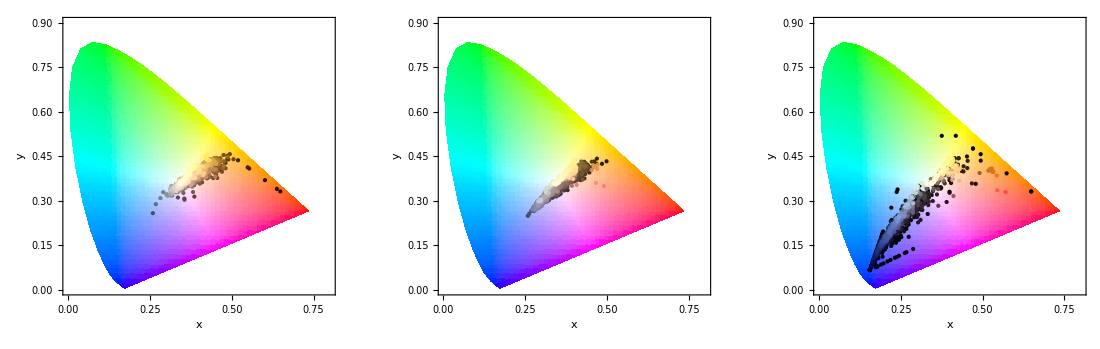

```mathematica
GraphicsRow[Show[ChromaticityPlot[#],plotCircles]&/@imgABC,ImageSize->1100]
```

```mathematica
imgABCTrim=ImageTrim[#, {{100,100},{500,900}}]&/@imgABC;
MapThread[Labeled[Image[#1],#2]&,{imgABCTrim,{"Trim A","Trim B","Trim C"}}]
```

{-Graphics-Trim A,-Graphics-Trim B,-Graphics-Trim C}

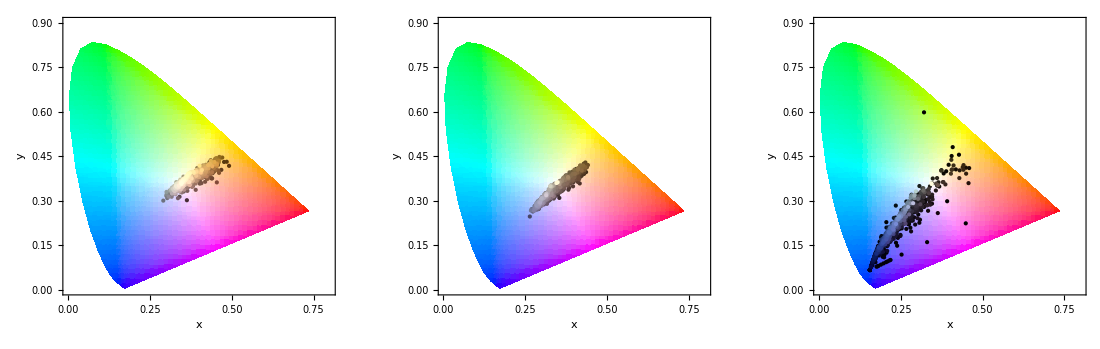

```mathematica
GraphicsRow[Show[ChromaticityPlot[#],plotCircles]&/@imgABCTrim,ImageSize->1100]
```

{-Graphics-,-Graphics-,-Graphics-}

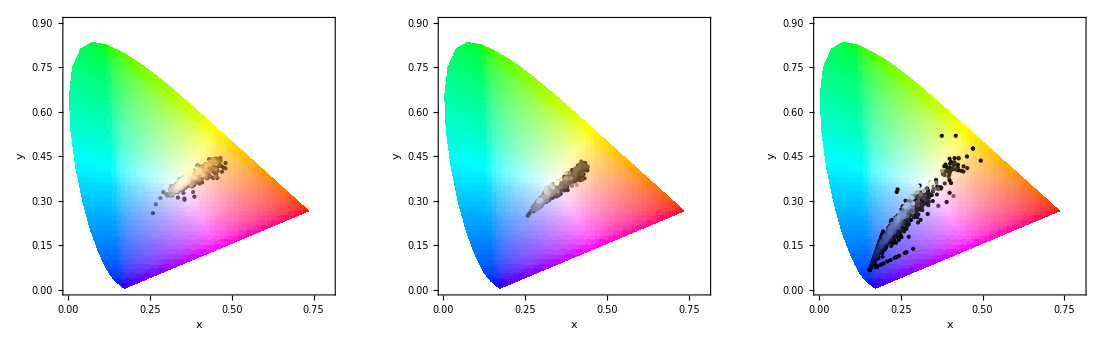

```mathematica
alpha=Import[StringJoin[NotebookDirectory[],"Dress no background.png"]];
background=White;
img10alpha=Binarize[ColorNegate@alpha,0.99];
imgABCNoBackground=ImageMultiply[ImageAdd[#,img10alpha],ImageAdd[ColorNegate@img10alpha,background]]&/@imgABC
GraphicsRow[Show[ChromaticityPlot[#],plotCircles]&/@imgABCNoBackground,ImageSize->1100]
```